```mathematica
neConditions = symbolicNashEquilibria[alicesScores/.{a->0,b->0}//Simplify,bobsScores/.{a-> 0,b->0}//Simplify]//Simplify//MatrixForm
```

Set::shape: Lists {m$12837,n$12837} and {} are not the same shape.

Do::iterb: Iterator {i0,m$12837} does not have appropriate bounds.

{}

```mathematica
neConditions = symbolicNashEquilibria[alicesScores/.{a->0,b->0}//Simplify,bobsScores/.{a-> 0,b->0}//Simplify]//Simplify//MatrixForm
```

(False | False | False | False
False | False | False | False
False | False | False | Cos[2 γ]+5 Sin[γ]^2≤2
False | False | Cos[2 γ]+5 Sin[γ]^2≤2 | False)

```mathematica
neConditions = symbolicNashEquilibria[alicesScores/.{a->b}//Simplify,bobsScores/.{a-> b}//Simplify]//Simplify//TrigToExp//FullSimplify;
```

```mathematica
neConditions = symbolicNashEquilibria[alicesScores//Simplify,bobsScores//Simplify]//TrigReduce//Simplify;
```

```mathematica
GraphicsGrid[Table[DensityPlot3D[alicesScores[[i,j]]/.{a->b},{a,-10,10},{b,-10,10},{γ,0,Pi/4},RegionFunction->Function[{A,B,G,z},neConditions[[i]][[j]]/.{a->A,b->B,γ->G}],Ticks->None,ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False],{i,4},{j,4}]]
```

```mathematica
DensityPlot3D[alicesScores[[3,4]]/.{a->b},{a,-10,10},{b,-10,10},{γ,0,Pi/4},Ticks->None,ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
Manipulate[DensityPlot[alicesScores[[2,4]]/.{a->b},{a,0,5},{b,0,5},ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False],{γ,0,Pi/4}]
```

```mathematica
DensityPlot3D[alicesScores[[i,j]]/.{a->b},{a,-10,10},{b,-10,10},{γ,0,Pi/4},RegionFunction->Function[{A,B,G,z},neConditions[[i]][[j]]/.{a->A,b->B,γ->G}],Ticks->None,ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False]/.{i->4,j->4}
```

-Graphics3D-

```mathematica
neConditions//MatrixForm
```

(False | False | False | False
False | 6 Cos[2 γ]+16 Cos[2 a γ]≥7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]&&Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]≤0&&12 Cos[2 a γ]≥6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]&&6 Cos[2 γ]+16 Cos[2 b γ]≥6 Cos[2 a γ]+Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ]&&6 Cos[2 a γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≤0&&12 Cos[2 b γ]≥6 Cos[2 γ]+6 Cos[2 a γ]+Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ] | 6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≥16 Cos[2 a γ]+6 Cos[2 b γ]&&Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≥6 Cos[2 b γ]&&7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≥6 (Cos[2 γ]+2 Cos[2 a γ]+Cos[2 b γ])&&6 Cos[2 γ]+6 Cos[2 a γ]+Cos[2 (a-b) γ]+16 Cos[2 b γ]+Cos[2 (a+b) γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&6 Cos[2 a γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≥0&&6 Cos[2 a γ]+Cos[2 (a-b) γ]+12 Cos[2 b γ]+Cos[2 (a+b) γ]≥6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ]) | 3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 Cos[2 b γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 (5+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≥0&&12 Cos[2 b γ]≤6 Cos[2 γ]+6 Cos[2 a γ]+Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ]&&6 Cos[2 a γ]+Cos[2 (a-b) γ]+12 Cos[2 b γ]+Cos[2 (a+b) γ]≤6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])
False | 6 Cos[2 γ]+16 Cos[2 a γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]≥0&&12 Cos[2 a γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]≥6 Cos[2 γ]+7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&6 Cos[2 γ]+Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ]≥6 Cos[2 a γ]+16 Cos[2 b γ]&&Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≥6 Cos[2 a γ]&&Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ]≥6 (Cos[2 γ]+Cos[2 a γ]+2 Cos[2 b γ]) | 6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+6 Cos[2 b γ]≥16 Cos[2 a γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]&&6 Cos[2 b γ]≥Cos[2 (a-b) γ]+Cos[2 (a+b) γ]&&7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+6 Cos[2 b γ]≥6 Cos[2 γ]+12 Cos[2 a γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]&&6 Cos[2 γ]+6 Cos[2 a γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥Cos[2 (a-b) γ]+16 Cos[2 b γ]+Cos[2 (a+b) γ]&&6 Cos[2 a γ]≥Cos[2 (a-b) γ]+Cos[2 (a+b) γ]&&6 Cos[2 a γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥6 Cos[2 γ]+Cos[2 (a-b) γ]+12 Cos[2 b γ]+Cos[2 (a+b) γ] | 2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&Cos[2 b γ]≤3 Cos[2 γ]&&Cos[2 (a-b) γ]+7 Cos[2 (-1+b) γ]+7 Cos[2 (1+b) γ]+Cos[2 (a+b) γ]≤6 (Cos[2 γ]+Cos[2 a γ]+2 Cos[2 b γ])&&6 Cos[2 a γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤6 Cos[2 γ]+Cos[2 (a-b) γ]+12 Cos[2 b γ]+Cos[2 (a+b) γ]
False | 3 Cos[2 γ]+Cos[2 a γ]≥0&&12 Cos[2 a γ]≤6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]&&12 Cos[2 a γ]+Cos[2 (a-b) γ]+6 Cos[2 b γ]+Cos[2 (a+b) γ]≤6 Cos[2 γ]+7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≤2 Cos[2 a γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≤2 (5+Cos[2 a γ]) | Cos[2 a γ]≤3 Cos[2 γ]&&7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]≤6 (Cos[2 γ]+2 Cos[2 a γ]+Cos[2 b γ])&&7 Cos[2 (-1+a) γ]+7 Cos[2 (1+a) γ]+6 Cos[2 b γ]≤6 Cos[2 γ]+12 Cos[2 a γ]+Cos[2 (a-b) γ]+Cos[2 (a+b) γ]&&2 Cos[2 a γ]≤3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&2 (7 Cos[2 γ]+Cos[2 a γ])≤10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ] | 14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥2 (5+Cos[2 b γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≥10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥2 (5+Cos[2 a γ])&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ])

```mathematica
neConditions[[2,3]]
```

1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥22 Cos[2 b γ]&&1+Cos[4 b γ]≥6 Cos[2 b γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 (Cos[2 γ]+3 Cos[2 b γ])&&1+6 Cos[2 γ]+22 Cos[2 b γ]+Cos[4 b γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&1+6 Cos[2 b γ]+Cos[4 b γ]≥0&&1+18 Cos[2 b γ]+Cos[4 b γ]≥6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])

```mathematica
FindInstance[Simplify[neConditions[[1]][[2]],Assumptions->{0<γ<π/2,0<b<5}],{γ,b}]
neConditions[[2]][[1]]//Simplify
```

```mathematica
TrigReduce[neConditions[[1]][[2]]]
Refine[neConditions[[1]][[2]]]
```

False

False

```mathematica
Table[neConditions[[2]][[1]]/.γ->G,{G,0,Pi/2,Pi/100}]
```

{False,3+Cos[π/100]^2 Cos[(b π)/50]≤2 Cos[π/50]+Cos[(b π)/100]^2 Sin[π/100]^2&&(1+3 Cos[π/50]) Cos[(b π)/50]≤0&&7 Cos[(b π)/50]≤3&&(-3+Cos[π/50]) Cos[(b π)/50]≥3 Cos[π/100]^2 Sin[(b π)/100]^2&&3 Cos[π/50]+Cos[(b π)/50]≤0,3+Cos[π/50]^2 Cos[(b π)/25]≤2 Cos[π/25]+Cos[(b π)/50]^2 Sin[π/50]^2&&(1+3 Cos[π/25]) Cos[(b π)/25]≤0&&7 Cos[(b π)/25]≤3&&(-3+Cos[π/25]) Cos[(b π)/25]≥3 Cos[π/50]^2 Sin[(b π)/50]^2&&3 Cos[π/25]+Cos[(b π)/25]≤0,3+Cos[(3 π)/100]^2 Cos[(3 b π)/50]≤2 Cos[(3 π)/50]+Cos[(3 b π)/100]^2 Sin[(3 π)/100]^2&&(1+3 Cos[(3 π)/50]) Cos[(3 b π)/50]≤0&&7 Cos[(3 b π)/50]≤3&&(-3+Cos[(3 π)/50]) Cos[(3 b π)/50]≥3 Cos[(3 π)/100]^2 Sin[(3 b π)/100]^2&&3 Cos[(3 π)/50]+Cos[(3 b π)/50]≤0,3+Cos[π/25]^2 Cos[(2 b π)/25]≤2 Cos[(2 π)/25]+Cos[(b π)/25]^2 Sin[π/25]^2&&(1+3 Cos[(2 π)/25]) Cos[(2 b π)/25]≤0&&7 Cos[(2 b π)/25]≤3&&(-3+Cos[(2 π)/25]) Cos[(2 b π)/25]≥3 Cos[π/25]^2 Sin[(b π)/25]^2&&3 Cos[(2 π)/25]+Cos[(2 b π)/25]≤0,3+Cos[π/20]^2 Cos[(b π)/10]≤2 √(5/8+(√5)/8)+Cos[(b π)/20]^2 Sin[π/20]^2&&(1+3 √(5/8+(√5)/8)) Cos[(b π)/10]≤0&&7 Cos[(b π)/10]≤3&&(-3+√(5/8+(√5)/8)) Cos[(b π)/10]≥3 Cos[π/20]^2 Sin[(b π)/20]^2&&3 √(5/8+(√5)/8)+Cos[(b π)/10]≤0,3+Cos[(3 π)/50]^2 Cos[(3 b π)/25]≤2 Cos[(3 π)/25]+Cos[(3 b π)/50]^2 Sin[(3 π)/50]^2&&(1+3 Cos[(3 π)/25]) Cos[(3 b π)/25]≤0&&7 Cos[(3 b π)/25]≤3&&(-3+Cos[(3 π)/25]) Cos[(3 b π)/25]≥3 Cos[(3 π)/50]^2 Sin[(3 b π)/50]^2&&3 Cos[(3 π)/25]+Cos[(3 b π)/25]≤0,3+Cos[(7 π)/100]^2 Cos[(7 b π)/50]≤2 Cos[(7 π)/50]+Cos[(7 b π)/100]^2 Sin[(7 π)/100]^2&&(1+3 Cos[(7 π)/50]) Cos[(7 b π)/50]≤0&&7 Cos[(7 b π)/50]≤3&&(-3+Cos[(7 π)/50]) Cos[(7 b π)/50]≥3 Cos[(7 π)/100]^2 Sin[(7 b π)/100]^2&&3 Cos[(7 π)/50]+Cos[(7 b π)/50]≤0,3+Cos[(2 π)/25]^2 Cos[(4 b π)/25]≤2 Cos[(4 π)/25]+Cos[(2 b π)/25]^2 Sin[(2 π)/25]^2&&(1+3 Cos[(4 π)/25]) Cos[(4 b π)/25]≤0&&7 Cos[(4 b π)/25]≤3&&(-3+Cos[(4 π)/25]) Cos[(4 b π)/25]≥3 Cos[(2 π)/25]^2 Sin[(2 b π)/25]^2&&3 Cos[(4 π)/25]+Cos[(4 b π)/25]≤0,3+Cos[(9 π)/100]^2 Cos[(9 b π)/50]≤2 Cos[(9 π)/50]+Cos[(9 b π)/100]^2 Sin[(9 π)/100]^2&&(1+3 Cos[(9 π)/50]) Cos[(9 b π)/50]≤0&&7 Cos[(9 b π)/50]≤3&&(-3+Cos[(9 π)/50]) Cos[(9 b π)/50]≥3 Cos[(9 π)/100]^2 Sin[(9 b π)/100]^2&&3 Cos[(9 π)/50]+Cos[(9 b π)/50]≤0,3+(5/8+(√5)/8) Cos[(b π)/5]≤1/2 (1+√5)+1/16 (-1+√5)^2 Cos[(b π)/10]^2&&(1+3/4 (1+√5)) Cos[(b π)/5]≤0&&7 Cos[(b π)/5]≤3&&(-3+1/4 (1+√5)) Cos[(b π)/5]≥3 (5/8+(√5)/8) Sin[(b π)/10]^2&&3/4 (1+√5)+Cos[(b π)/5]≤0,3+Cos[(11 π)/100]^2 Cos[(11 b π)/50]≤2 Cos[(11 π)/50]+Cos[(11 b π)/100]^2 Sin[(11 π)/100]^2&&(1+3 Cos[(11 π)/50]) Cos[(11 b π)/50]≤0&&7 Cos[(11 b π)/50]≤3&&(-3+Cos[(11 π)/50]) Cos[(11 b π)/50]≥3 Cos[(11 π)/100]^2 Sin[(11 b π)/100]^2&&3 Cos[(11 π)/50]+Cos[(11 b π)/50]≤0,3+Cos[(3 π)/25]^2 Cos[(6 b π)/25]≤2 Cos[(6 π)/25]+Cos[(3 b π)/25]^2 Sin[(3 π)/25]^2&&(1+3 Cos[(6 π)/25]) Cos[(6 b π)/25]≤0&&7 Cos[(6 b π)/25]≤3&&(-3+Cos[(6 π)/25]) Cos[(6 b π)/25]≥3 Cos[(3 π)/25]^2 Sin[(3 b π)/25]^2&&3 Cos[(6 π)/25]+Cos[(6 b π)/25]≤0,3+Cos[(13 π)/100]^2 Cos[(13 b π)/50]≤Cos[(13 b π)/100]^2 Sin[(13 π)/100]^2+2 Sin[(6 π)/25]&&Cos[(13 b π)/50] (1+3 Sin[(6 π)/25])≤0&&7 Cos[(13 b π)/50]≤3&&Cos[(13 b π)/50] (-3+Sin[(6 π)/25])≥3 Cos[(13 π)/100]^2 Sin[(13 b π)/100]^2&&Cos[(13 b π)/50]+3 Sin[(6 π)/25]≤0,3+Cos[(7 π)/50]^2 Cos[(7 b π)/25]≤Cos[(7 b π)/50]^2 Sin[(7 π)/50]^2+2 Sin[(11 π)/50]&&Cos[(7 b π)/25] (1+3 Sin[(11 π)/50])≤0&&7 Cos[(7 b π)/25]≤3&&Cos[(7 b π)/25] (-3+Sin[(11 π)/50])≥3 Cos[(7 π)/50]^2 Sin[(7 b π)/50]^2&&Cos[(7 b π)/25]+3 Sin[(11 π)/50]≤0,3+Cos[(3 π)/20]^2 Cos[(3 b π)/10]≤2 √(5/8-(√5)/8)+Cos[(3 b π)/20]^2 Sin[(3 π)/20]^2&&(1+3 √(5/8-(√5)/8)) Cos[(3 b π)/10]≤0&&7 Cos[(3 b π)/10]≤3&&(-3+√(5/8-(√5)/8)) Cos[(3 b π)/10]≥3 Cos[(3 π)/20]^2 Sin[(3 b π)/20]^2&&3 √(5/8-(√5)/8)+Cos[(3 b π)/10]≤0,3+Cos[(4 π)/25]^2 Cos[(8 b π)/25]≤Cos[(4 b π)/25]^2 Sin[(4 π)/25]^2+2 Sin[(9 π)/50]&&Cos[(8 b π)/25] (1+3 Sin[(9 π)/50])≤0&&7 Cos[(8 b π)/25]≤3&&Cos[(8 b π)/25] (-3+Sin[(9 π)/50])≥3 Cos[(4 π)/25]^2 Sin[(4 b π)/25]^2&&Cos[(8 b π)/25]+3 Sin[(9 π)/50]≤0,3+Cos[(17 π)/100]^2 Cos[(17 b π)/50]≤2 Sin[(4 π)/25]+Cos[(17 b π)/100]^2 Sin[(17 π)/100]^2&&Cos[(17 b π)/50] (1+3 Sin[(4 π)/25])≤0&&7 Cos[(17 b π)/50]≤3&&Cos[(17 b π)/50] (-3+Sin[(4 π)/25])≥3 Cos[(17 π)/100]^2 Sin[(17 b π)/100]^2&&Cos[(17 b π)/50]+3 Sin[(4 π)/25]≤0,3+Cos[(9 π)/50]^2 Cos[(9 b π)/25]≤2 Sin[(7 π)/50]+Cos[(9 b π)/50]^2 Sin[(9 π)/50]^2&&Cos[(9 b π)/25] (1+3 Sin[(7 π)/50])≤0&&7 Cos[(9 b π)/25]≤3&&Cos[(9 b π)/25] (-3+Sin[(7 π)/50])≥3 Cos[(9 π)/50]^2 Sin[(9 b π)/50]^2&&Cos[(9 b π)/25]+3 Sin[(7 π)/50]≤0,3+Cos[(19 π)/100]^2 Cos[(19 b π)/50]≤2 Sin[(3 π)/25]+Cos[(19 b π)/100]^2 Sin[(19 π)/100]^2&&Cos[(19 b π)/50] (1+3 Sin[(3 π)/25])≤0&&7 Cos[(19 b π)/50]≤3&&Cos[(19 b π)/50] (-3+Sin[(3 π)/25])≥3 Cos[(19 π)/100]^2 Sin[(19 b π)/100]^2&&Cos[(19 b π)/50]+3 Sin[(3 π)/25]≤0,3+1/16 (1+√5)^2 Cos[(2 b π)/5]≤1/2 (-1+√5)+(5/8-(√5)/8) Cos[(b π)/5]^2&&(1+3/4 (-1+√5)) Cos[(2 b π)/5]≤0&&7 Cos[(2 b π)/5]≤3&&(-3+1/4 (-1+√5)) Cos[(2 b π)/5]≥3/16 (1+√5)^2 Sin[(b π)/5]^2&&3/4 (-1+√5)+Cos[(2 b π)/5]≤0,3+Cos[(21 π)/100]^2 Cos[(21 b π)/50]≤2 Sin[(2 π)/25]+Cos[(21 b π)/100]^2 Sin[(21 π)/100]^2&&Cos[(21 b π)/50] (1+3 Sin[(2 π)/25])≤0&&7 Cos[(21 b π)/50]≤3&&Cos[(21 b π)/50] (-3+Sin[(2 π)/25])≥3 Cos[(21 π)/100]^2 Sin[(21 b π)/100]^2&&Cos[(21 b π)/50]+3 Sin[(2 π)/25]≤0,3+Cos[(11 π)/50]^2 Cos[(11 b π)/25]≤2 Sin[(3 π)/50]+Cos[(11 b π)/50]^2 Sin[(11 π)/50]^2&&Cos[(11 b π)/25] (1+3 Sin[(3 π)/50])≤0&&7 Cos[(11 b π)/25]≤3&&Cos[(11 b π)/25] (-3+Sin[(3 π)/50])≥3 Cos[(11 π)/50]^2 Sin[(11 b π)/50]^2&&Cos[(11 b π)/25]+3 Sin[(3 π)/50]≤0,3+Cos[(23 π)/100]^2 Cos[(23 b π)/50]≤2 Sin[π/25]+Cos[(23 b π)/100]^2 Sin[(23 π)/100]^2&&Cos[(23 b π)/50] (1+3 Sin[π/25])≤0&&7 Cos[(23 b π)/50]≤3&&Cos[(23 b π)/50] (-3+Sin[π/25])≥3 Cos[(23 π)/100]^2 Sin[(23 b π)/100]^2&&Cos[(23 b π)/50]+3 Sin[π/25]≤0,3+Cos[(6 π)/25]^2 Cos[(12 b π)/25]≤2 Sin[π/50]+Cos[(6 b π)/25]^2 Sin[(6 π)/25]^2&&Cos[(12 b π)/25] (1+3 Sin[π/50])≤0&&7 Cos[(12 b π)/25]≤3&&Cos[(12 b π)/25] (-3+Sin[π/50])≥3 Cos[(6 π)/25]^2 Sin[(6 b π)/25]^2&&Cos[(12 b π)/25]+3 Sin[π/50]≤0,3+1/2 Cos[(b π)/2]≤1/2 Cos[(b π)/4]^2&&Cos[(b π)/2]≤0&&7 Cos[(b π)/2]≤3&&-3 Cos[(b π)/2]≥3/2 Sin[(b π)/4]^2&&Cos[(b π)/2]≤0,3+Cos[(13 b π)/25] Sin[(6 π)/25]^2≤Cos[(6 π)/25]^2 Cos[(13 b π)/50]^2-2 Sin[π/50]&&Cos[(13 b π)/25] (1-3 Sin[π/50])≤0&&7 Cos[(13 b π)/25]≤3&&Cos[(13 b π)/25] (-3-Sin[π/50])≥3 Sin[(6 π)/25]^2 Sin[(13 b π)/50]^2&&Cos[(13 b π)/25]-3 Sin[π/50]≤0,3+Cos[(27 b π)/50] Sin[(23 π)/100]^2≤Cos[(23 π)/100]^2 Cos[(27 b π)/100]^2-2 Sin[π/25]&&Cos[(27 b π)/50] (1-3 Sin[π/25])≤0&&7 Cos[(27 b π)/50]≤3&&Cos[(27 b π)/50] (-3-Sin[π/25])≥3 Sin[(23 π)/100]^2 Sin[(27 b π)/100]^2&&Cos[(27 b π)/50]-3 Sin[π/25]≤0,3+Cos[(14 b π)/25] Sin[(11 π)/50]^2≤Cos[(11 π)/50]^2 Cos[(7 b π)/25]^2-2 Sin[(3 π)/50]&&Cos[(14 b π)/25] (1-3 Sin[(3 π)/50])≤0&&7 Cos[(14 b π)/25]≤3&&Cos[(14 b π)/25] (-3-Sin[(3 π)/50])≥3 Sin[(11 π)/50]^2 Sin[(7 b π)/25]^2&&Cos[(14 b π)/25]-3 Sin[(3 π)/50]≤0,3+Cos[(29 b π)/50] Sin[(21 π)/100]^2≤Cos[(21 π)/100]^2 Cos[(29 b π)/100]^2-2 Sin[(2 π)/25]&&Cos[(29 b π)/50] (1-3 Sin[(2 π)/25])≤0&&7 Cos[(29 b π)/50]≤3&&Cos[(29 b π)/50] (-3-Sin[(2 π)/25])≥3 Sin[(21 π)/100]^2 Sin[(29 b π)/100]^2&&Cos[(29 b π)/50]-3 Sin[(2 π)/25]≤0,3+(5/8-(√5)/8) Cos[(3 b π)/5]≤1/2 (1-√5)+1/16 (1+√5)^2 Cos[(3 b π)/10]^2&&(1+3/4 (1-√5)) Cos[(3 b π)/5]≤0&&7 Cos[(3 b π)/5]≤3&&(-3+1/4 (1-√5)) Cos[(3 b π)/5]≥3 (5/8-(√5)/8) Sin[(3 b π)/10]^2&&3/4 (1-√5)+Cos[(3 b π)/5]≤0,3+Cos[(31 b π)/50] Sin[(19 π)/100]^2≤Cos[(19 π)/100]^2 Cos[(31 b π)/100]^2-2 Sin[(3 π)/25]&&Cos[(31 b π)/50] (1-3 Sin[(3 π)/25])≤0&&7 Cos[(31 b π)/50]≤3&&Cos[(31 b π)/50] (-3-Sin[(3 π)/25])≥3 Sin[(19 π)/100]^2 Sin[(31 b π)/100]^2&&Cos[(31 b π)/50]-3 Sin[(3 π)/25]≤0,3+Cos[(16 b π)/25] Sin[(9 π)/50]^2≤Cos[(9 π)/50]^2 Cos[(8 b π)/25]^2-2 Sin[(7 π)/50]&&Cos[(16 b π)/25] (1-3 Sin[(7 π)/50])≤0&&7 Cos[(16 b π)/25]≤3&&Cos[(16 b π)/25] (-3-Sin[(7 π)/50])≥3 Sin[(9 π)/50]^2 Sin[(8 b π)/25]^2&&Cos[(16 b π)/25]-3 Sin[(7 π)/50]≤0,3+Cos[(33 b π)/50] Sin[(17 π)/100]^2≤Cos[(17 π)/100]^2 Cos[(33 b π)/100]^2-2 Sin[(4 π)/25]&&Cos[(33 b π)/50] (1-3 Sin[(4 π)/25])≤0&&7 Cos[(33 b π)/50]≤3&&Cos[(33 b π)/50] (-3-Sin[(4 π)/25])≥3 Sin[(17 π)/100]^2 Sin[(33 b π)/100]^2&&Cos[(33 b π)/50]-3 Sin[(4 π)/25]≤0,3+Cos[(17 b π)/25] Sin[(4 π)/25]^2≤Cos[(4 π)/25]^2 Cos[(17 b π)/50]^2-2 Sin[(9 π)/50]&&Cos[(17 b π)/25] (1-3 Sin[(9 π)/50])≤0&&7 Cos[(17 b π)/25]≤3&&Cos[(17 b π)/25] (-3-Sin[(9 π)/50])≥3 Sin[(4 π)/25]^2 Sin[(17 b π)/50]^2&&Cos[(17 b π)/25]-3 Sin[(9 π)/50]≤0,3+Cos[(7 b π)/10] Sin[(3 π)/20]^2≤-2 √(5/8-(√5)/8)+Cos[(3 π)/20]^2 Cos[(7 b π)/20]^2&&(1-3 √(5/8-(√5)/8)) Cos[(7 b π)/10]≤0&&7 Cos[(7 b π)/10]≤3&&(-3-√(5/8-(√5)/8)) Cos[(7 b π)/10]≥3 Sin[(3 π)/20]^2 Sin[(7 b π)/20]^2&&-3 √(5/8-(√5)/8)+Cos[(7 b π)/10]≤0,3+Cos[(18 b π)/25] Sin[(7 π)/50]^2≤Cos[(7 π)/50]^2 Cos[(9 b π)/25]^2-2 Sin[(11 π)/50]&&Cos[(18 b π)/25] (1-3 Sin[(11 π)/50])≤0&&7 Cos[(18 b π)/25]≤3&&Cos[(18 b π)/25] (-3-Sin[(11 π)/50])≥3 Sin[(7 π)/50]^2 Sin[(9 b π)/25]^2&&Cos[(18 b π)/25]-3 Sin[(11 π)/50]≤0,3+Cos[(37 b π)/50] Sin[(13 π)/100]^2≤Cos[(13 π)/100]^2 Cos[(37 b π)/100]^2-2 Sin[(6 π)/25]&&Cos[(37 b π)/50] (1-3 Sin[(6 π)/25])≤0&&7 Cos[(37 b π)/50]≤3&&Cos[(37 b π)/50] (-3-Sin[(6 π)/25])≥3 Sin[(13 π)/100]^2 Sin[(37 b π)/100]^2&&Cos[(37 b π)/50]-3 Sin[(6 π)/25]≤0,3+Cos[(19 b π)/25] Sin[(3 π)/25]^2≤-2 Cos[(6 π)/25]+Cos[(3 π)/25]^2 Cos[(19 b π)/50]^2&&(1-3 Cos[(6 π)/25]) Cos[(19 b π)/25]≤0&&7 Cos[(19 b π)/25]≤3&&(-3-Cos[(6 π)/25]) Cos[(19 b π)/25]≥3 Sin[(3 π)/25]^2 Sin[(19 b π)/50]^2&&-3 Cos[(6 π)/25]+Cos[(19 b π)/25]≤0,3+Cos[(39 b π)/50] Sin[(11 π)/100]^2≤-2 Cos[(11 π)/50]+Cos[(11 π)/100]^2 Cos[(39 b π)/100]^2&&(1-3 Cos[(11 π)/50]) Cos[(39 b π)/50]≤0&&7 Cos[(39 b π)/50]≤3&&(-3-Cos[(11 π)/50]) Cos[(39 b π)/50]≥3 Sin[(11 π)/100]^2 Sin[(39 b π)/100]^2&&-3 Cos[(11 π)/50]+Cos[(39 b π)/50]≤0,3+1/16 (-1+√5)^2 Cos[(4 b π)/5]≤1/2 (-1-√5)+(5/8+(√5)/8) Cos[(2 b π)/5]^2&&(1+3/4 (-1-√5)) Cos[(4 b π)/5]≤0&&7 Cos[(4 b π)/5]≤3&&(-3+1/4 (-1-√5)) Cos[(4 b π)/5]≥3/16 (-1+√5)^2 Sin[(2 b π)/5]^2&&3/4 (-1-√5)+Cos[(4 b π)/5]≤0,3+Cos[(41 b π)/50] Sin[(9 π)/100]^2≤-2 Cos[(9 π)/50]+Cos[(9 π)/100]^2 Cos[(41 b π)/100]^2&&(1-3 Cos[(9 π)/50]) Cos[(41 b π)/50]≤0&&7 Cos[(41 b π)/50]≤3&&(-3-Cos[(9 π)/50]) Cos[(41 b π)/50]≥3 Sin[(9 π)/100]^2 Sin[(41 b π)/100]^2&&-3 Cos[(9 π)/50]+Cos[(41 b π)/50]≤0,3+Cos[(21 b π)/25] Sin[(2 π)/25]^2≤-2 Cos[(4 π)/25]+Cos[(2 π)/25]^2 Cos[(21 b π)/50]^2&&(1-3 Cos[(4 π)/25]) Cos[(21 b π)/25]≤0&&7 Cos[(21 b π)/25]≤3&&(-3-Cos[(4 π)/25]) Cos[(21 b π)/25]≥3 Sin[(2 π)/25]^2 Sin[(21 b π)/50]^2&&-3 Cos[(4 π)/25]+Cos[(21 b π)/25]≤0,3+Cos[(43 b π)/50] Sin[(7 π)/100]^2≤-2 Cos[(7 π)/50]+Cos[(7 π)/100]^2 Cos[(43 b π)/100]^2&&(1-3 Cos[(7 π)/50]) Cos[(43 b π)/50]≤0&&7 Cos[(43 b π)/50]≤3&&(-3-Cos[(7 π)/50]) Cos[(43 b π)/50]≥3 Sin[(7 π)/100]^2 Sin[(43 b π)/100]^2&&-3 Cos[(7 π)/50]+Cos[(43 b π)/50]≤0,3+Cos[(22 b π)/25] Sin[(3 π)/50]^2≤-2 Cos[(3 π)/25]+Cos[(3 π)/50]^2 Cos[(11 b π)/25]^2&&(1-3 Cos[(3 π)/25]) Cos[(22 b π)/25]≤0&&7 Cos[(22 b π)/25]≤3&&(-3-Cos[(3 π)/25]) Cos[(22 b π)/25]≥3 Sin[(3 π)/50]^2 Sin[(11 b π)/25]^2&&-3 Cos[(3 π)/25]+Cos[(22 b π)/25]≤0,3+Cos[(9 b π)/10] Sin[π/20]^2≤-2 √(5/8+(√5)/8)+Cos[π/20]^2 Cos[(9 b π)/20]^2&&(1-3 √(5/8+(√5)/8)) Cos[(9 b π)/10]≤0&&7 Cos[(9 b π)/10]≤3&&(-3-√(5/8+(√5)/8)) Cos[(9 b π)/10]≥3 Sin[π/20]^2 Sin[(9 b π)/20]^2&&-3 √(5/8+(√5)/8)+Cos[(9 b π)/10]≤0,3+Cos[(23 b π)/25] Sin[π/25]^2≤-2 Cos[(2 π)/25]+Cos[π/25]^2 Cos[(23 b π)/50]^2&&(1-3 Cos[(2 π)/25]) Cos[(23 b π)/25]≤0&&7 Cos[(23 b π)/25]≤3&&(-3-Cos[(2 π)/25]) Cos[(23 b π)/25]≥3 Sin[π/25]^2 Sin[(23 b π)/50]^2&&-3 Cos[(2 π)/25]+Cos[(23 b π)/25]≤0,3+Cos[(47 b π)/50] Sin[(3 π)/100]^2≤-2 Cos[(3 π)/50]+Cos[(3 π)/100]^2 Cos[(47 b π)/100]^2&&(1-3 Cos[(3 π)/50]) Cos[(47 b π)/50]≤0&&7 Cos[(47 b π)/50]≤3&&(-3-Cos[(3 π)/50]) Cos[(47 b π)/50]≥3 Sin[(3 π)/100]^2 Sin[(47 b π)/100]^2&&-3 Cos[(3 π)/50]+Cos[(47 b π)/50]≤0,3+Cos[(24 b π)/25] Sin[π/50]^2≤-2 Cos[π/25]+Cos[π/50]^2 Cos[(12 b π)/25]^2&&(1-3 Cos[π/25]) Cos[(24 b π)/25]≤0&&7 Cos[(24 b π)/25]≤3&&(-3-Cos[π/25]) Cos[(24 b π)/25]≥3 Sin[π/50]^2 Sin[(12 b π)/25]^2&&-3 Cos[π/25]+Cos[(24 b π)/25]≤0,3+Cos[(49 b π)/50] Sin[π/100]^2≤-2 Cos[π/50]+Cos[π/100]^2 Cos[(49 b π)/100]^2&&(1-3 Cos[π/50]) Cos[(49 b π)/50]≤0&&7 Cos[(49 b π)/50]≤3&&(-3-Cos[π/50]) Cos[(49 b π)/50]≥3 Sin[π/100]^2 Sin[(49 b π)/100]^2&&-3 Cos[π/50]+Cos[(49 b π)/50]≤0,3≤-2+Cos[(b π)/2]^2&&-2 Cos[b π]≤0&&7 Cos[b π]≤3&&-4 Cos[b π]≥0&&-3+Cos[b π]≤0}

```mathematica
Manipulate[Plot[Cos[γ]^2 (6-4 Cos[2 b γ])+6 Cos[b γ]^2 Sin[γ]^2+(-9+Cos[2 b γ]) Sin[b γ]^2,{γ,0,Pi/2},PlotRange->{-5,5}],{b,0,100}]
```

```mathematica
alicesScores[[3,4]]
```

Cos[γ]^2 Cos[b γ]^2-(-4+Cos[2 b γ]) Sin[γ]^2

```mathematica
neConditions[[3]][[4]]
```

2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&Cos[2 b γ]≤3 Cos[2 γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≤6 (Cos[2 γ]+3 Cos[2 b γ])&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]

```mathematica
,
```

```mathematica
neConditions[[3,4]]
```

2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&Cos[2 b γ]≤3 Cos[2 γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≤6 (Cos[2 γ]+3 Cos[2 b γ])&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]

```mathematica
Function[{b,γ},neConditions[[3,4]]]
```

Function[{b,γ},neConditions⟦3,4⟧]

```mathematica
region[1,1]
```

False

```mathematica
region[B_,G_,t_]:=neConditions[[3]][[4]]/.{b->B,γ->G}
```

```mathematica
neConditions[[3]][[4]]
```

2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&Cos[2 b γ]≤3 Cos[2 γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≤6 (Cos[2 γ]+3 Cos[2 b γ])&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]

```mathematica
DensityPlot[alicesScores[[3,4]],{b,-10,10},{γ,0,Pi/4},RegionFunction->Function[{B,G,z},neConditions[[3]][[4]]/.{b->B,γ->G}]]
```

-Graphics-

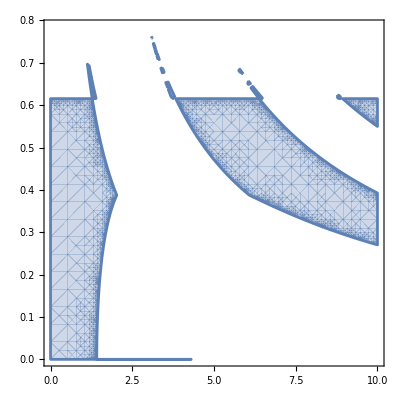

```mathematica
RegionPlot[neConditions[[3]][[4]],{b,0,10},{γ,0,Pi/4},MaxRecursion->7]
```

```mathematica
alicesScores//MatrixForm
```

(3 | 3 Cos[γ]^2 Cos[a γ]^2+(3-2 Cos[2 a γ]) Sin[γ]^2 | 5 Cos[a γ]^2 Sin[γ]^2+(2+Cos[2 γ]) Sin[a γ]^2 | 0
-Cos[γ]^2 (-4+Cos[2 b γ])+Cos[b γ]^2 Sin[γ]^2 | -Cos[a γ]^2 (-4+Cos[2 b γ])+Sin[a γ]^2 Sin[b γ]^2 | 3 Cos[b γ]^2 Sin[a γ]^2+(3-2 Cos[2 a γ]) Sin[b γ]^2 | 5 Cos[b γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[b γ]^2
Cos[γ]^2 (4+Cos[2 b γ])+Sin[γ]^2 Sin[b γ]^2 | Cos[a γ]^2 (4+Cos[2 b γ])+Cos[b γ]^2 Sin[a γ]^2 | Cos[a γ]^2 Cos[b γ]^2+(4+Cos[2 b γ]) Sin[a γ]^2 | Cos[γ]^2 Cos[b γ]^2-(-4+Cos[2 b γ]) Sin[γ]^2
5 | Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2 | Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2 | 1)

```mathematica
GraphicsGrid[Table[DensityPlot[alicesScores[[i,j]]/.{a->b},{b,-10,10},{γ,0,Pi/2},BoundaryStyle->Red,MaxRecursion->5],{i,4},{j,4}]]
```

$Aborted

```mathematica
If[neConditions[[2,4]],alicesScores[[2,4]]]
```

3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 Cos[2 b γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 (5+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≥0&&6 Cos[2 b γ]≤1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&1+18 Cos[2 b γ]+Cos[4 b γ]≤6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])

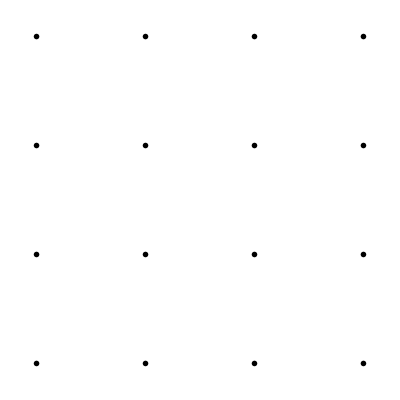

```mathematica
GraphicsGrid[Table[DensityPlot[alicesScores[[i,j]]/.{a->b},{b,-10,10},{γ,0,Pi/4},RegionFunction->Function[{B,G,z},neConditionsAndSame[[i]][[j]]/.{b->B,γ->G}],MaxRecursion->2,Frame->False,Ticks->None,ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False],{i,4},{j,4}]]
```

```mathematica
bobsScores
```

{{3,-Cos[γ]^2 (-4+Cos[2 a γ])+Cos[a γ]^2 Sin[γ]^2,Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2,5},{3 Cos[γ]^2 Cos[b γ]^2+(3-2 Cos[2 b γ]) Sin[γ]^2,3 Cos[a γ]^2 Cos[b γ]^2+(3+2 Cos[2 b γ]) Sin[a γ]^2,Cos[a γ]^2 (3+2 Cos[2 b γ])+3 Cos[b γ]^2 Sin[a γ]^2,Cos[γ]^2 (3+2 Cos[2 b γ])+3 Sin[γ]^2 Sin[b γ]^2},{5 Cos[b γ]^2 Sin[γ]^2+(2+Cos[2 γ]) Sin[b γ]^2,Cos[b γ]^2 Sin[a γ]^2-(-4+Cos[2 a γ]) Sin[b γ]^2,Cos[a γ]^2 (3-2 Cos[2 b γ])+3 Sin[a γ]^2 Sin[b γ]^2,Cos[γ]^2 (3-2 Cos[2 b γ])+3 Cos[b γ]^2 Sin[γ]^2},{0,5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2,Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2,1}}

```mathematica
GraphicsGrid[Table[DensityPlot[bobsScores[[i,j]]/.{a->b},{b,-10,10},{γ,2ArcTan[√(5-2 √6)],Pi/4},RegionFunction->Function[{B,G,z},neConditions[[i]][[j]]/.{b->B,γ->G}],MaxRecursion->2,Frame->False,Ticks->None,ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False],{i,4},{j,4}]]
```

```mathematica
DensityPlot[bobsScores[[3,4]]/.{a->b},{b,-10,10},{γ,2ArcTan[√(5-2 √6)],Pi/4},RegionFunction->Function[{B,G,z},neConditions[[3]][[4]]/.{b->B,γ->G}],ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False,MaxRecursion->5]
```

$Aborted

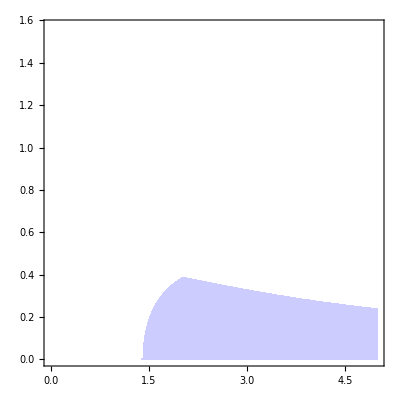

```mathematica
DensityPlot[bobsScores[[4,4]]/.{a->b},{b,0,5},{γ,0,Pi/2},RegionFunction->Function[{B,G,z},neConditionsAndSame[[4]][[4]]/.{b->B,γ->G}],ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False,MaxRecursion->3]
```

```mathematica
neConditionsAndSame = Table[neConditions[[i,j]]&&alicesScores[[i,j]]==bobsScores[[i,j]],{i,4},{j,4}]//TrigReduce//Simplify
```

{{False,False,False,False},{False,Cos[2 a γ]==Cos[2 b γ]&&1+6 Cos[2 b γ]+Cos[4 b γ]≤0&&6 Cos[2 γ]+10 Cos[2 b γ]≥1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&6 Cos[2 b γ]≥1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ],1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥22 Cos[2 b γ]&&1+Cos[4 b γ]≥6 Cos[2 b γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 (Cos[2 γ]+3 Cos[2 b γ])&&1+6 Cos[2 γ]+22 Cos[2 b γ]+Cos[4 b γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&1+6 Cos[2 b γ]+Cos[4 b γ]≥0&&1+18 Cos[2 b γ]+Cos[4 b γ]≥6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&Cos[2 a γ]+Cos[2 b γ]==0,3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 Cos[2 b γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 (5+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≥0&&6 Cos[2 b γ]≤1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&1+18 Cos[2 b γ]+Cos[4 b γ]≤6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 Cos[2 γ]+Cos[2 (-1+b) γ]+Cos[2 (1+b) γ]==0},{False,1+6 Cos[2 γ]+22 Cos[2 b γ]+Cos[4 b γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&1+6 Cos[2 b γ]+Cos[4 b γ]≥0&&1+18 Cos[2 b γ]+Cos[4 b γ]≥6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥22 Cos[2 b γ]&&1+Cos[4 b γ]≥6 Cos[2 b γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 (Cos[2 γ]+3 Cos[2 b γ])&&Cos[2 a γ]+Cos[2 b γ]==0,Cos[2 a γ]==Cos[2 b γ]&&1+Cos[4 b γ]≤6 Cos[2 b γ]&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]&&6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥1+10 Cos[2 b γ]+Cos[4 b γ],2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&Cos[2 b γ]≤3 Cos[2 γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≤6 (Cos[2 γ]+3 Cos[2 b γ])&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]&&2 Cos[2 γ]==Cos[2 (-1+b) γ]+Cos[2 (1+b) γ]},{False,3 Cos[2 γ]+Cos[2 b γ]≥0&&6 Cos[2 b γ]≤1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&1+18 Cos[2 b γ]+Cos[4 b γ]≤6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 Cos[2 b γ]&&14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤2 (5+Cos[2 b γ])&&2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]==0,Cos[2 b γ]≤3 Cos[2 γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≤6 (Cos[2 γ]+3 Cos[2 b γ])&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]&&2 Cos[2 b γ]≤3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≤10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]&&2 Cos[2 γ]==Cos[2 (-1+a) γ]+Cos[2 (1+a) γ],14 Cos[2 γ]+3 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥2 (5+Cos[2 b γ])&&2 (7 Cos[2 γ]+Cos[2 b γ])≥10+3 Cos[2 (-1+b) γ]+3 Cos[2 (1+b) γ]}}

```mathematica
DynamicModule[{pt={0,0}},Column[{EventHandler[DensityPlot[bobsScores[[4,4]]/. {a->b},{b,0,5},{γ,0,Pi/2},RegionFunction->Function[{B,G,z},neConditionsAndSame[[4]][[4]]/. {b->B,γ->G}],ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False,MaxRecursion->3],"MouseMoved":>(pt=MousePosition["Graphics"])],Dynamic[Module[{val1,val2},val1=bobsScores[[4,4]]/. {a->b}/. {b->pt[[1]],γ->pt[[2]]};
val2=alicesScores[[4,4]]/. {a->b}/. {b->pt[[1]],γ->pt[[2]]};
Row[{"Coordinates: ",pt,"   Value: ",NumberForm[val1,{4,3}],"alices: ",NumberForm[val2,{4,3}]}]]]}]]
```

```mathematica
GraphicsGrid[Table[RegionPlot[(alicesScores[[i,j]]/.{a->b})==bobsScores[[i,j]]/.{a->b},{b,-1,1},{γ,0,.3},MaxRecursion->3],{i,4},{j,4}]]
```

-Graphics-

RegionPlot::argrx: RegionPlot called with 2 arguments; 3 arguments are expected.

General::stop: Further output of RegionPlot::argrx will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

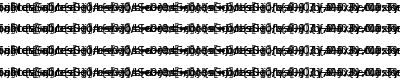

```mathematica
GraphicsGrid[Table[RegionPlot[(alicesScores[[i,j]]/.{a->0,b->0})==bobsScores[[i,j]]/.{a->0,b->0},{γ,0,.3},MaxRecursion->3],{i,4},{j,4}]]
```

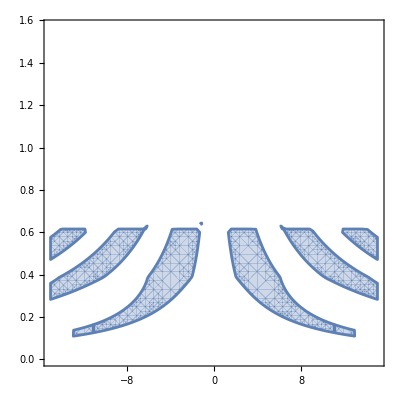
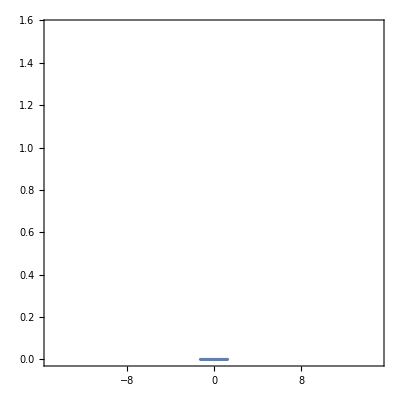
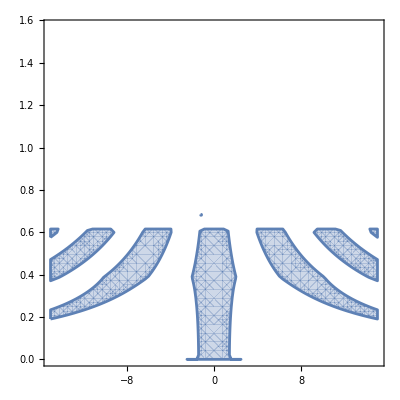
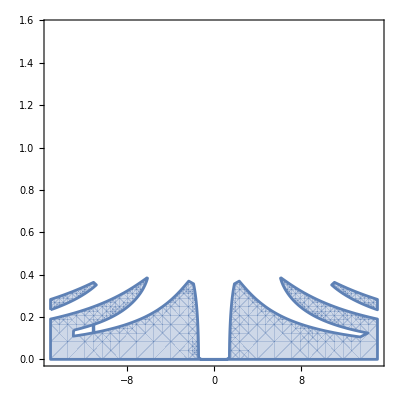
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[RegionPlot[neConditions[[i]][[j]],{b,-15,15},{γ,0,Pi/2},MaxRecursion->3],{i,4},{j,4}]
```

```mathematica
alicesScores[[3,4]]/.{a->0,b->0}
```

Cos[γ]^2+3 Sin[γ]^2

```mathematica
bobsScores[[3,4]]/.{a->0,b->0}
```

Cos[γ]^2+3 Sin[γ]^2

```mathematica
neConditions = symbolicNashEquilibria[alicesScores/.{a->b}//Simplify,bobsScores/.{a-> b}//Simplify]//Simplify;
```

```mathematica
neConditions//MatrixForm
```

(False | 6 Cos[2 γ]+10 Cos[2 b γ]≤1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&2 (3-2 Cos[2 b γ]) Sin[γ]^2≥Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≤0&&5+Cos[γ]^2 (-4+Cos[2 b γ])≤Cos[b γ]^2 Sin[γ]^2&&(1+3 Cos[2 γ]) Cos[2 b γ]≤0 | 10 Cos[b γ]^2 Sin[γ]^2+(-5+2 Cos[2 γ]+Cos[2 b γ]) Sin[b γ]^2≥0&&Cos[4 b γ]+40 Cos[b γ]^2 Sin[γ]^2+8 Cos[2 γ] Sin[b γ]^2≥9&&3 Cos[2 γ]≤Cos[2 b γ]&&Cos[γ]^2 (4+Cos[2 b γ])+Sin[γ]^2 Sin[b γ]^2≥5&&(1+3 Cos[2 γ]) Cos[2 b γ]≥0 | False
5+Cos[γ]^2 (-4+Cos[2 b γ])≤Cos[b γ]^2 Sin[γ]^2&&(1+3 Cos[2 γ]) Cos[2 b γ]≤0&&6 Cos[2 γ]+10 Cos[2 b γ]≤1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&2 (3-2 Cos[2 b γ]) Sin[γ]^2≥Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≤0 | 1+6 Cos[2 b γ]+Cos[4 b γ]≤0&&6 Cos[2 γ]+10 Cos[2 b γ]≥1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&6 Cos[2 b γ]≥1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ] | 10 Cos[b γ]^2 Sin[γ]^2+(-5+2 Cos[2 γ]+Cos[2 b γ]) Sin[b γ]^2≤0&&1+Cos[4 b γ]≥6 Cos[2 b γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 (Cos[2 γ]+3 Cos[2 b γ])&&1/2 Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])+(-3+2 Cos[2 b γ]) Sin[γ]^2≥0&&1+6 Cos[2 b γ]+Cos[4 b γ]≥0&&1/2 Cos[b γ]^2 (9+Cos[2 b γ])≥Cos[γ]^2 (3+2 Cos[2 b γ])+3 Sin[γ]^2 Sin[b γ]^2 | (-1+3 Cos[2 γ]) Cos[2 b γ]≤0&&5 Cos[b γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[b γ]^2&&3 Cos[2 γ]+Cos[2 b γ]≥0&&1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 Cos[2 b γ]&&Cos[γ]^2 (3+2 Cos[2 b γ])+3 Sin[γ]^2 Sin[b γ]^2≥1/2 Cos[b γ]^2 (9+Cos[2 b γ])
Cos[γ]^2 (4+Cos[2 b γ])+Sin[γ]^2 Sin[b γ]^2≥5&&(1+3 Cos[2 γ]) Cos[2 b γ]≥0&&10 Cos[b γ]^2 Sin[γ]^2+(-5+2 Cos[2 γ]+Cos[2 b γ]) Sin[b γ]^2≥0&&6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≤1+10 Cos[2 b γ]+Cos[4 b γ]&&3 Cos[2 γ]≤Cos[2 b γ] | 1/2 Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])+(-3+2 Cos[2 b γ]) Sin[γ]^2≥0&&1+6 Cos[2 b γ]+Cos[4 b γ]≥0&&1/2 Cos[b γ]^2 (9+Cos[2 b γ])≥Cos[γ]^2 (3+2 Cos[2 b γ])+3 Sin[γ]^2 Sin[b γ]^2&&10 Cos[b γ]^2 Sin[γ]^2+(-5+2 Cos[2 γ]+Cos[2 b γ]) Sin[b γ]^2≤0&&1+Cos[4 b γ]≥6 Cos[2 b γ]&&1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 (Cos[2 γ]+3 Cos[2 b γ]) | Cos[b γ]^4+(2-Cos[2 γ]+Cos[2 b γ]) Sin[b γ]^2≥5 Cos[b γ]^2 Sin[γ]^2&&Cos[2 b γ]≥0&&Cos[b γ]^4+(4+Cos[2 b γ]) Sin[b γ]^2≥Cos[γ]^2 (3-2 Cos[2 b γ])+3 Cos[b γ]^2 Sin[γ]^2&&6 Cos[2 γ]+7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥1+10 Cos[2 b γ]+Cos[4 b γ]&&1+Cos[4 b γ]≤6 Cos[2 b γ]&&7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])≥1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ] | (-1+3 Cos[2 γ]) Cos[2 b γ]≥0&&Cos[γ]^2 Cos[b γ]^2≥1+(-4+Cos[2 b γ]) Sin[γ]^2&&3 Cos[2 γ]≥Cos[2 b γ]&&Cos[γ]^2 (6-4 Cos[2 b γ])+6 Cos[b γ]^2 Sin[γ]^2+(-9+Cos[2 b γ]) Sin[b γ]^2≥0&&1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])
False | 3 Cos[2 γ]+Cos[2 b γ]≥0&&1+6 Cos[2 γ]+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]≥6 Cos[2 b γ]&&Cos[γ]^2 (3+2 Cos[2 b γ])+3 Sin[γ]^2 Sin[b γ]^2≥1/2 Cos[b γ]^2 (9+Cos[2 b γ])&&(-1+3 Cos[2 γ]) Cos[2 b γ]≤0&&5 Cos[b γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[b γ]^2 | 3 Cos[2 γ]≥Cos[2 b γ]&&Cos[γ]^2 (6-4 Cos[2 b γ])+6 Cos[b γ]^2 Sin[γ]^2+(-9+Cos[2 b γ]) Sin[b γ]^2≥0&&1+6 Cos[2 γ]+6 Cos[2 b γ]+Cos[4 b γ]≥7 (Cos[2 (-1+b) γ]+Cos[2 (1+b) γ])&&(-1+3 Cos[2 γ]) Cos[2 b γ]≥0&&Cos[γ]^2 Cos[b γ]^2≥1+(-4+Cos[2 b γ]) Sin[γ]^2 | 1+(-4+Cos[2 b γ]) Sin[γ]^2≥Cos[γ]^2 Cos[b γ]^2&&1+(-2+Cos[2 γ]) Sin[b γ]^2≥5 Cos[b γ]^2 Sin[γ]^2)

6 Cos[2 γ]+10 Cos[2 b γ]≤1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&2 (3-2 Cos[2 b γ]) Sin[γ]^2≥Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≤0&&5+Cos[γ]^2 (-4+Cos[2 b γ])≤Cos[b γ]^2 Sin[γ]^2&&(1+3 Cos[2 γ]) Cos[2 b γ]≤0

```mathematica
FullSimplify[neConditions[[1,2]],Assumptions->{γ∈Reals,b∈Reals}]
```

6 Cos[2 γ]+10 Cos[2 b γ]≤1+7 Cos[2 (-1+b) γ]+Cos[4 b γ]+7 Cos[2 (1+b) γ]&&2 (3-2 Cos[2 b γ]) Sin[γ]^2≥Cos[b γ]^2 (6-3 Cos[2 γ]+Cos[2 b γ])&&3 Cos[2 γ]+Cos[2 b γ]≤0&&5+Cos[γ]^2 (-4+Cos[2 b γ])≤Cos[b γ]^2 Sin[γ]^2&&(1+3 Cos[2 γ]) Cos[2 b γ]≤0

```mathematica
Manipulate[DensityPlot[If[(1+3 Cos[2 γ]) Cos[2 b γ]<=l,1,0],{b,0,10},{γ,0,Pi/2}],{l,-10,10}]
```